```mathematica
Question 15
```

```mathematica
ClearAll[list15,plots15,integrals15,PlotFunction15]
```

```mathematica
list15={Integrate[1,{y,y,2-y}],Integrate[1,{y,y/2,2}],Integrate[1,{y,y,Log[y]}]}
```

{2-2 y,2-y/2,-y+Log[y]}

```mathematica
{2-2 y,2-y/2,-y+Log[y]}
```

{2-2 y,2-y/2,-y+Log[y]}

```mathematica
plots15 = {}
```

{}

```mathematica
PlotFunction15[z_,a_,b_]:=AppendTo[plots15,Plot[z,{y,a,b},Filling->Axis]]
```

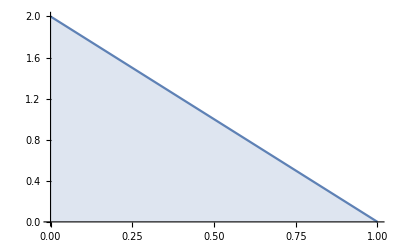

```mathematica
PlotFunction15[list15[[1]],0,1]
```

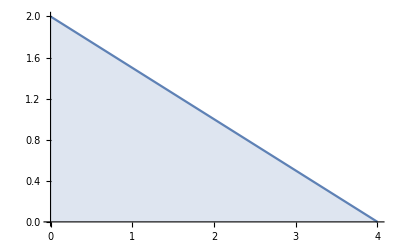
{-Graphics-,-Graphics-}

```mathematica
PlotFunction15[list15[[2]],0,4]
```

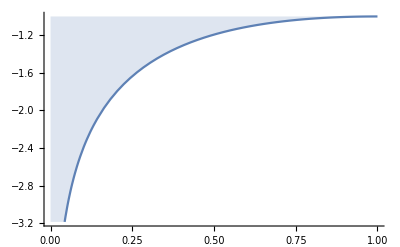
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[plots15,Plot[list15[[3]],{y,0,1},Filling->Top]]
```

```mathematica
plots15
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
integrals15={Integrate[list15[[1]],{y,0,1}],Integrate[list15[[2]],{y,0,4}],Integrate[list15[[3]],{y,1,2}]}
```

{1,4,-5/2+Log[4]}

```mathematica
grid15=Grid[Transpose[{list15,plots15,integrals15}],Frame->All]
```

2-2 y | -Graphics- | 1
2-y/2 | -Graphics- | 4
-y+Log[y] | -Graphics- | -5/2+Log[4]